```mathematica
Np=1;
Id=Table[KroneckerDelta[k1,k1p],{k1,0,Np},{k1p,0,Np}];
Sx=Table[KroneckerDelta[k1+1,k1p]*Sqrt[(k1+1)*(Np-k1)]+KroneckerDelta[k1,k1p+1]*Sqrt[(k1p+1)*(Np-k1p)],{k1,0,Np},{k1p,0,Np}];
Sy=Table[-I*KroneckerDelta[k1+1,k1p]*Sqrt[(k1+1)*(Np-k1)]+I*KroneckerDelta[k1,k1p+1]*Sqrt[(k1p+1)*(Np-k1p)],{k1,0,Np},{k1p,0,Np}];
Sz=Table[KroneckerDelta[k1,k1p]*(2*k1-Np),{k1,0,Np},{k1p,0,Np}];
ghzstate=ArrayReshape[Table[KroneckerDelta[k1,k2,k3],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]];
ghzstate=N[Normalize[ghzstate]];
psi0[k1_,k2_,k3_]=(1/Sqrt[2]^(3*Np))*Sqrt[Binomial[Np,k1]*Binomial[Np,k2]*Binomial[Np,k3]];
psi1[k1_,k2_,k3_]=(1/Sqrt[Np+1])*KroneckerDelta[k1,k2]*(1/Sqrt[2]^(Np))*Sqrt[Binomial[Np,k3]];
Urotzx1=MatrixExp[I*Sy*Pi/4];
Urotzx=KroneckerProduct[Urotzx1,Urotzx1,Urotzx1];
Urotxz=ConjugateTranspose[Urotzx];
Idbig=KroneckerProduct[Id,Id,Id];
psivec0=ArrayReshape[Table[psi1[k1,k2,k3],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]];Hamz=2*(KroneckerProduct[Sz.Sz,Id,Id]+KroneckerProduct[Id,Sz.Sz,Id]+KroneckerProduct[Id,Id,Sz.Sz])-2*(KroneckerProduct[Sz,Sz,Id]+KroneckerProduct[Sz,Id,Sz]+KroneckerProduct[Id,Sz,Sz]);
Hamx1=MatrixPower[(-KroneckerProduct[Sz,Id,Id]-KroneckerProduct[Id,Sz,Id]+KroneckerProduct[Id,Id,Sz]+Np*Idbig),2];
Hamx2=(-KroneckerProduct[Sz,Id,Id]+KroneckerProduct[Id,Sz,Id]-KroneckerProduct[Id,Id,Sz]+Np*Idbig)^2;
Hamx3=(KroneckerProduct[Sz,Id,Id]+KroneckerProduct[Id,Sz,Id]+KroneckerProduct[Id,Id,Sz]+Np*Idbig)^2;
Hamx4=(KroneckerProduct[Sz,Id,Id]-KroneckerProduct[Id,Sz,Id]-KroneckerProduct[Id,Id,Sz]+Np*Idbig)^2;
```

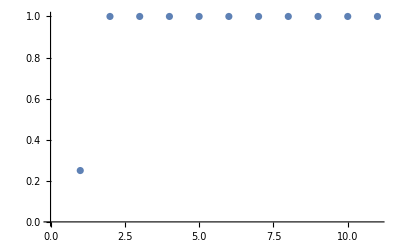

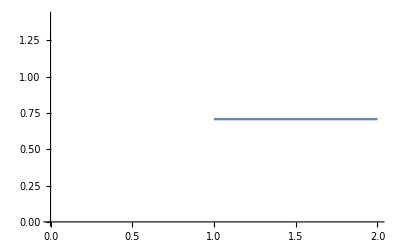

final psi={0.707107,0,0,0,0,0,0,0.707107}

ghz={0.707107,0.,0.,0.,0.,0.,0.,0.707107}

1.

```mathematica
t=10.0;
nrounds=10;
projmatx=Urotzx.MatrixExp[-Hamx1*t].Urotxz;
projmatz=MatrixExp[-Hamz*t];
psi=Normalize[ArrayReshape[Table[psi0[k1,k2,k3],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]]];
fidlist={Abs[Conjugate[ghzstate].psi]^2};
For[n=1,n≤nrounds,n=n+1,
psi=Normalize[projmatz.projmatx.psi];
fidlist=Append[fidlist,Abs[Conjugate[ghzstate].psi]^2];
];
psielem=Table[ArrayReshape[psi,{Np+1,Np+1,Np+1}][[k,k,k]],{k,1,Np+1}];
p1=ListPlot[fidlist];
Print[p1];
p2=ListPlot[psielem,Joined->True];
Print[p2];
Print["final psi=",Chop[psi]];
Print["ghz=",ghzstate];
Print[Last[fidlist]];
```

```mathematica
psielem
```

{0.450244,0.545234,0.545234,0.450244}

```mathematica
psicomp=Normalize[Table[N[Binomial[Np,k]^(0.30)],{k,0,Np}]]
```

{0.412872,0.574053,0.574053,0.412872}

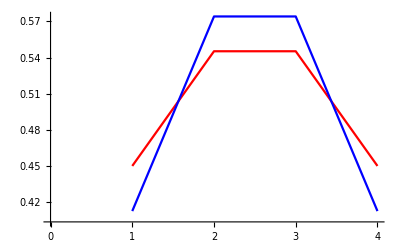

```mathematica
ListPlot[{psielem,psicomp},Joined->True,PlotStyle->{Red,Blue}]
```

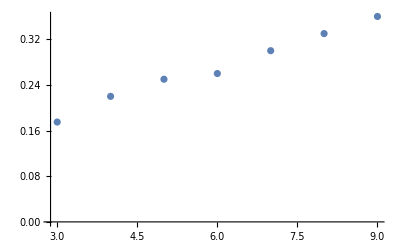

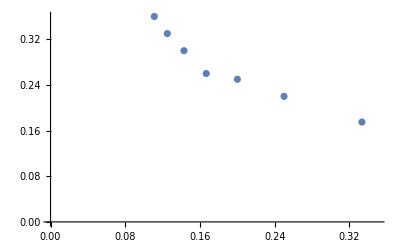

```mathematica
powerlist={{3,0.175},{4,0.22},{5,0.25},{6,0.26},{7,0.3},{8,0.33},{9,0.36}};
powerlist2=Table[{1/powerlist[[n]][[1]],powerlist[[n]][[2]]},{n,1,Length[powerlist]}];
ListPlot[powerlist]
ListPlot[powerlist2,PlotRange->{{0,0.35},All}]
```

```mathematica
Eigensystem[Hamx3]
```

{{64,36,36,36,16,16,16,16,16,16,16,4,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
psitemp=Normalize[1.0*ArrayReshape[Table[psi0[k1,k2,k3],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]]];
```

```mathematica
psitemp
```

{0.125,0.176777,0.125,0.176777,0.25,0.176777,0.125,0.176777,0.125,0.176777,0.25,0.176777,0.25,0.353553,0.25,0.176777,0.25,0.176777,0.125,0.176777,0.125,0.176777,0.25,0.176777,0.125,0.176777,0.125}

```mathematica
projmatx.psitemp
```

{0.125,0.176777,0.125,0.176777,0.25,0.176777,0.125,0.176777,0.125,0.176777,0.25,0.176777,0.25,0.353553,0.25,0.176777,0.25,0.176777,0.125,0.176777,0.125,0.176777,0.25,0.176777,0.125,0.176777,0.125}

```mathematica
psitemp.Chop[projmatx.psitemp]
```

1.